```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica

```mathematica
LECsNUCL=Import["./LECs_nucl_Joki.dat","Table"][[2;;]];

logspace[increments_,start_?Positive,end_?Positive]:=Exp@Range[Log@start,Log@end,Log[end/start]/increments];

activeLEC=LECsNUCL[[All,{1,2,3}]];
hbar=197.327053;
Mm=938.92;
m1=2 Mm;m2= Mm;
μ=m1 m2/(m1+m2);
mh2=(2Mm)/(hbar)^2;
Print[1/mh2]
```

20.7355

```mathematica
(*a1 r1^2+b1 r2^2+ c1 (r1+r2)^2*)
I1[lam_,a1_,a2_,b1_,b2_,c1_,c2_] :=(2 Pi)^3/(8((a1+a2+c1+c2+lam)(b1+b2+c1+c2+lam)-(c1+c2-lam)^2)^1.5)+(2 Pi)^3/(8((a1+a2+c1+c2+4lam)(b1+b2+c1+c2+lam)-(c1+c2+2lam)^2)^1.5)+(2 Pi)^3/(8((a1+a2+c1+c2+lam)(b1+b2+c1+c2+4lam)-(c1+c2+2lam)^2)^1.5);
I2[lam_,a1_,a2_,b1_,b2_,c1_,c2_] :=(2 Pi)^3/(8((a1+a2+c1+c2+5lam)(b1+b2+c1+c2+2lam)-(c1+c2+lam)^2)^1.5);
I3[a1_,a2_,b1_,b2_,c1_,c2_] :=(8/3) ((2 Pi)^3/(32 ((a1+a2+c1+c2)(b1+b2+c1+c2)-(c1+c2)^2)^2.5))((a2 c1+c2 a1+2c1 c2+2a1 a2)(b1+c1+b2+c2)+(b1 c2+b2 c1+2c1 c2+2b1 b2)(a1+a2+c1+c2)-(c2(a1+b1)+c1(a2+b2)-b2 a1-a2 b1+4c1 c2)(c1+c2));
(*I1[lam_,a1_,a2_,b1_,b2_,c1_,c2_] :=(2 Pi)^3/((4(a1+a2+lam)(b1+b2+lam)-(c1+c2-2lam)^2)^1.5)+(2 Pi)^3/((4(a1+a2+4lam)(b1+b2+lam)-(c1+c2+4lam)^2)^1.5)+(2 Pi)^3/((4(a1+a2+lam)(b1+b2+4lam)-(c1+c2+4lam)^2)^1.5);
I2[lam_,a1_,a2_,b1_,b2_,c1_,c2_] :=(2 Pi)^3/((4(a1+a2+5lam)(b1+b2+2lam)-(c1+c2+2lam)^2)^1.5);
I3[a1_,a2_,b1_,b2_,c1_,c2_] :=8/3(2 Pi)^3/(8((a1+a2+c1+c2)(b1+b2+c1+c2)-(c1+c2)^2)^1.5)((a2 c1+c2 a1+2c1 c2+2a1 a2)(b1+c1+b2+c2)+(b1 c2+b2 c1+2c1 c2+2b1 b2)(a1+a2+c1+c2)-(c2(a1+b1)+c1(a2+b2)-b2 a1-a2 b1+4c1 c2)(c1+c2))*)

(*I1[lam_,a1_,a2_,b1_,b2_,c1_,c2_] :=3(2 Pi)^3/(8((a1+a2+c1+c2+lam)^2-(c1+c2-lam)^2)^1.5);
I2[lam_,a1_,a2_,b1_,b2_,c1_,c2_] :=(2 Pi)^3/(8((a1+a2+c1+c2+5lam)(a1+a2+c1+c2+2lam)-(c1+c2+lam)^2)^1.5);
I3[a1_,a2_,b1_,b2_,c1_,c2_] :=(2 Pi)^3/(64/9((2a1 a2+a2 c1+2c1 c2+c2 a1)^2)-16/9(4c1 c2+a2 c1+a1 c2+c1 a2+c2 a1-a2 a1-a1 a2)^2)^1.5;*)

(*a1 r1^2+b1 r2^2+ c1 r1 r2*)
(*I1[lam_,a1_,a2_,b1_,b2_,c1_,c2_] :=(2 Pi)^3/((4(a1+a2+lam^2/4)(b1+b2+lam^2/4)-(c1+c2-2lam^2/4)^2)^1.5)+(2 Pi)^3/((4(a1+a2+4lam^2/4)(b1+b2+lam^2/4)-(c1+c2+4lam^2/4)^2)^1.5)+(2 Pi)^3/((4(a1+a2+lam^2/4)(b1+b2+4lam^2/4)-(c1+c2+4lam^2/4)^2)^1.5);
I2[lam_,a1_,a2_,b1_,b2_,c1_,c2_] :=(2 Pi)^3/((4(a1+a2+2lam^2/4)(b1+b2+5lam^2/4)-(c1+c2+2lam^2/4)^2)^1.5);
I1[lam_,a1_,a2_,b1_,b2_,c1_,c2_] :=(2 Pi)^3/((4(a1+a2)(b1+b2)-(c1+c2)^2)^1.5)((8/3a1 a2+2/3 c1 c2-2/3a2 c1-2/3a1 c2)2(b1+b2)+(8/3 b1 b2+2/3c1 c2-2/3b1 c2-2/3 b2 c1)2(a1+a2)-4/3(a2(c1-b1)+a1(c2-b2)+b2 c1+c2 b1)(c1 +c2));*)
```

```mathematica
I3["α_1","α_2","α_3","α_4","α_5","α_6"]
```

(8 ((α_3+α_4+α_5+α_6) (2 α_1 α_2+α_2 α_5+α_1 α_6+2 α_5 α_6)+(α_1+α_2+α_5+α_6) (2 α_3 α_4+α_4 α_5+α_3 α_6+2 α_5 α_6)-(α_5+α_6) (-α_2 α_3-α_1 α_4+(α_2+α_4) α_5+(α_1+α_3) α_6+4 α_5 α_6)) π^3)/(3 (-(α_5+α_6)^2+(α_1+α_2+α_5+α_6) (α_3+α_4+α_5+α_6))^1.5)

```mathematica
ham[lam_,a1_,a2_,b1_,b2_,c1_,c2_,LECC_,LECD_,LECK_]:=Module[{locall=lam},
LECC I1[lam,a1,a2,b1,b2,c1,c2]+LECD I2[lam,a1,a2,b1,b2,c1,c2]+(LECK hbar^2/(2 Mm))I3[a1,a2,b1,b2,c1,c2]
]  ;
norm[a1_,a2_,b1_,b2_,c1_,c2_]:=Module[{},(2 Pi)^3/(8((a1+a2+c1+c2)(b1+b2+c1+c2)-(c1+c2)^2)^1.5)
]  ;
```

dimD:  bare basis dimension
widths: educated guess for the Gaussian width parameters each of which defines a bare basis function  e^(-β∑(r̄)^2)
lamd: cutoff/regularization parameter of the interaction
evlowthreshold: empirically determined threshold which sets the lower bound for the norm eigenvalues that are allowed in the
                                   stable, reduced basis

```mathematica
∑_cycl ∑_(i<j<k) Subscript[v, ijk]
```

C_0 = -1090.55       D_1 = 18879.1       E_kin factor = 3.

{-60.805,-3.46836,-0.211483}

{-60.2062,-2.72221,0.46536}

{-60.8553,-3.68011,-0.752903}

{-61.8178,-2.00162,-0.517608}

{-62.011,-2.98092,-0.471934}

{-60.7225,-2.01017,-1.16448}

{-60.9856,-4.74066,-1.57742}

{-61.5595,-2.48333,0.451533}

{-61.4063,-2.82478,-1.02717}

{-62.0286,-1.97851,-0.383123}

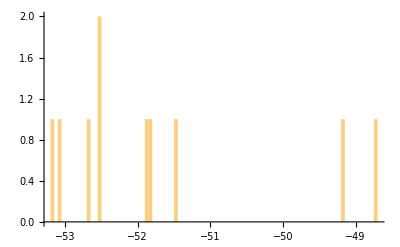

```mathematica
dimD=420;
lamd=6;

LECc=Flatten[Select[activeLEC,#[[1]]==lamd&]][[2]];
LECd=3 Flatten[Select[activeLEC,#[[1]]==lamd&]][[3]];
LECk=3.;
Print["C_0 = ",LECc,"       D_1 = ",LECd,"       E_kin factor = ",LECk];
limWu=25;
result={};nRuns=10;SetSharedVariable[result];

ParallelDo[
widths1 = RandomSample[N@logspace[dimD-1,0.005,limWu]];
widths2 = RandomSample[N@logspace[dimD-1,0.006,limWu]];
widths3 = RandomSample[N@logspace[dimD-1,0.008,limWu]];

hamm=Table[ham[lamd,widths1[[i]],widths1[[j]],widths2[[i]],widths2[[j]],widths3[[i]],widths3[[j]],LECc,LECd,LECk],{i,dimD},{j,dimD}];

normm=Table[norm[widths1[[i]],widths1[[j]],widths2[[i]],widths2[[j]],widths3[[i]],widths3[[j]]],{i,dimD},{j,dimD}];

esbare=Eigensystem[{hamm,normm}];
Print[Sort[esbare[[1]],Re[#1]<Re[#2]&][[;;3]]];

smallestAllowedNormEV=10^-4;
EVsysN=Eigensystem[normm];
{μ,transf}=Transpose[Select[Sort[Transpose[EVsysN],Re[#1][[1]]<Re[#2][[1]]&],#[[1]]>smallestAllowedNormEV&]];
trama=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);

EVsysH=Eigensystem[{(Transpose[trama].hamm).trama,(Transpose[trama].normm).trama}];
AppendTo[result,Sort[EVsysH[[1]],Re[#1]<Re[#2]&][[1]]];
(*Print["Eigenvalues StyleBox[\"HAMILTONIAN\",FontColor->RGBColor[1, 0, 0]]:   ",StringRiffle[Sort[EVsysH[[1]],Re[#1]<Re[#2]&][[;;2]]," "],"  ...  ",StringRiffle[Sort[EVsysH[[1]],Re[#1]<Re[#2]&][[-2;;]]," "]];*)
,{nn,1,nRuns}]
Histogram[result,100]
```